#### Data

```mathematica
Clear["Global`*"]
(*units and constants for trap depth mostly*)
kHz=10^3;
nm=10^-9;
mK=10^-3;
uK=10^-6;
us=10^-6;
kB=1.38064852 10^-23;
ℏ=1.0545718 10^-34;
amu=1.66054 10^-27;
λtrap=976 nm;
m=132.90545 amu;23amu;
Needs["ErrorBarLogPlots`"];
SetDirectory[NotebookDirectory[]];

params=Import["params.csv"][[1]];
survNonInt=Transpose[Import["surv.csv"]][[;;,4]]; 
survInt=Transpose[Import["surv.csv"]][[;;,2]]; 

survNonIntErr=Transpose[Import["survErr.csv"]][[;;,4]];
survIntErr=Transpose[Import["survErr.csv"]][[;;,2]];

(*only take the first half.. what are the 2 halves??*)

i=1;

dataNonInt=Thread[{Thread[{(params-((i-1)26+1)) ,survNonInt}],ErrorBar[#]&/@survNonIntErr}][[(i-1)26 +1;;i 26 ]];
dataInt=Thread[{Thread[{(params-((i-1)26+1)) ,survInt}],ErrorBar[#]&/@survIntErr}][[(i-1)26 +1;;i 26]];
```

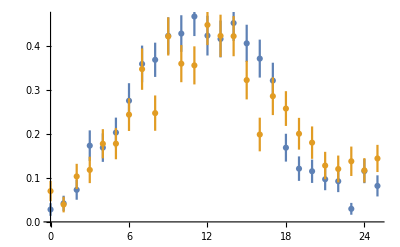

```mathematica
ErrorListPlot[{dataNonInt,dataInt}]
```

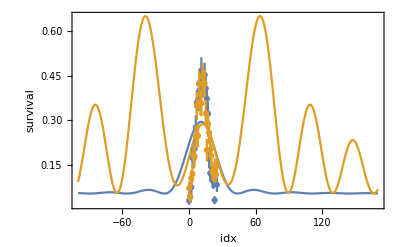

{Ω→5.45828,ω0→10.6954}

{Ω1→-4.27343,Ω2→63.6048,ω01→12.582,ω02→12.2474}

```mathematica
Clear[t];
Pe[ω_,ω0_,Ω_,t_,offs_]:=Ω^2/(Ω^2+(ω-ω0)^2)Sin[π t √(Ω^2+(ω-ω0)^2)]^2+offs;
t=30 10^-3;
offs=.0523;
nlmNonInt=NonlinearModelFit[dataNonInt[[;;,1]],Pe[ω,ω0,Ω,t,offs],{{Ω,10},{ω0,-10}},ω];
nlmInt=NonlinearModelFit[dataInt[[;;,1]],-offs+Pe[ω,ω01,Ω1,t,offs]+Pe[ω,ω02,Ω2,t,offs],{{Ω1,10},{Ω2,10},{ω01,-0},{ω02,55}},ω];

Show[{Plot[{nlmNonInt[ω],nlmInt[ω]},{ω,-100,170},PlotRange->All,
Axes->False,Frame->True,FrameLabel->{"idx","survival","i="<>ToString[i]},LabelStyle->{Black,17
}]
,
ErrorListPlot[{dataNonInt,dataInt}]}]
nlmNonInt["BestFitParameters"]
nlmInt["BestFitParameters"]
```

# also try overdriving but with interference from a component (=gnd state fraction) shifted by xyz kHz to left factor of 2pi??? expected shift:-13(7)kHz offs valid? is there interference? yes but waste of time to model...should just optimize OP does a nearby molecular state cause shift??? omega vs 2pi???